## Trajectory of Electron Through Berry Curvature

```mathematica
(*ClearAll["Global`*"];

ϵ=γ*kz[t]-√(kx[t]^2+ky[t]^2+kz[t]^2);
ϕ=-Ex*x[t];

r[t] = {x[t], y[t], z[t]};
k[t] = {kx[t], ky[t], kz[t]};
eqn1=D[r[t], t] -( Grad[ϵ, k[t]] +q*Cross[Grad[ϕ, r[t]], k[t] / (kx[t]^2+ky[t]^2+kz[t]^2)^(3/2)])
eqn2=D[k[t], t]+(Grad[ϕ, r[t]])*)
```

```mathematica
(*newr[t]={x[t], y[t], z[t]}/.DSolve[{eqn1[[1]]==0, eqn1[[2]]==0, eqn1[[3]]==0,
 eqn2[[1]]==0, eqn2[[2]]==0, eqn2[[3]]==0,
 x[0]==0, y[0]==0, z[0]==0,
 kx[0]==kx0, ky[0]==ky0, kz[0]==kz0},
{x[t], y[t], z[t], kx[t], ky[t], kz[t]}, t][[1]]*)
```

```mathematica
(*fontsize=50;

test1=newr[t]/.{kx0->1, ky0->1, kz0->1, Ex->0.1, q->1, γ->2};
test2=newr[t]/.{kx0->1, ky0->1, kz0->1, Ex->0.1, q->1, γ->3};
test3=newr[t]/.{kx0->1, ky0->1, kz0->1, Ex->0.1, q->1, γ->1};
ParametricPlot3D[{test3, test1, test2}, {t, 1, 34},
PlotRange->{{-50, 0}, {-50, 0}, {0, 50}},
ImageSize->{700, 700},
PlotStyle->{Directive[Thickness[0.007], Black], Directive[Thickness[0.007], Blue],Directive[Thickness[0.007], Green]},
PlotLegends->{"γ=1","γ=2", "γ=3"},
AxesLabel->{Style["x (a)", fontsize, Bold], Style["y (a)", fontsize, Bold], Style["z (a)",fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]}]*)
```

## Trajectory of Full Berry Curvature Term

```mathematica
ClearAll["Global`*"]

m=3.;
tz=1.;

vz = 0.0;
ec=1.0;
(* lattice spacing in natural units*)
alat=1.0;
gamma=2.0;
Ex=0.1;
Bvec={0.0, 0.0, 0.0}

(*Originally just kz0=0.1*)
kx0=0.1;
ky0=0.0;
kz0=0.0;

(* node separation along the z-axis (field direction) *)
dx[kx_,ky_,kz_]=-2Sin[kx];
dy[kx_,ky_,kz_]=-2Sin[ky];
dz[kx_,ky_,kz_]=(-2tz(Cos[kz]-Cos[k0])-m(2-Cos[kx]-Cos[ky])-vz ( Cos[3 kz]-Cos[3k0]));
ham[kx_,ky_,kz_]=gamma(Cos[kz]-Cos[k0])PauliMatrix[0]+dx[kx,ky,kz]PauliMatrix[1]+dy[kx,ky,kz]PauliMatrix[2]+dz[kx,ky,kz]PauliMatrix[3];
{nrgs1[kx_,ky_,kz_],nrgs2[kx_,ky_,kz_]}=FullSimplify[Eigenvalues[ham[kx,ky,kz]]];
dvec[kx_,ky_,kz_]={dx[kx,ky,kz],dy[kx,ky,kz],dz[kx,ky,kz]};

{gradE1[kx_,ky_,kz_],gradE2[kx_,ky_,kz_]}=alat*{{D[nrgs1[kx,ky,kz],kx],D[nrgs1[kx,ky,kz],ky],D[nrgs1[kx,ky,kz],kz]},{D[nrgs2[kx,ky,kz],kx],D[nrgs2[kx,ky,kz],ky],D[nrgs2[kx,ky,kz],kz]}};
{normE1[kx_,ky_,kz_],normE2[kx_,ky_,kz_]}={Norm[gradE1[kx,ky,kz]],Norm[gradE2[kx,ky,kz]]};
```

{0.,0.,0.}

```mathematica
Subscript[σ, x]= PauliMatrix[1];
Subscript[σ, y]= PauliMatrix[2];
Subscript[σ, z]= PauliMatrix[3];

H = -2*Sin[kx]*Subscript[σ, x]-2 *Sin[ky]*Subscript[σ, y]-(m*(2 - Cos[kx]-Cos[ky]) + 2 *tz*(Cos[kz] - Cos[k0]) + vz*(Cos[kz] -Cos[3*k0]))*Subscript[σ, z]+gamma*(Cos[kz] - Cos[k0])*PauliMatrix[0];

dvec = {-2*Sin[kx],-2 *Sin[ky],(m*(2 - Cos[kx]-Cos[ky]) + 2 *tz*(Cos[kz] - Cos[k0]) + vz*(Cos[kz] -Cos[3*k0]))};

kvec = {kx, ky, kz};

LeviCivita = LeviCivitaTensor[3];

Ωvec = {ωx, ωy, ωz};

denominator = FullSimplify[4*Norm[dvec]^3, Assumptions->{t>0, a>0, Subscript[t, z]>0, m>0,  Element[Subscript[k, x], Reals], Element[Subscript[k, y], Reals], Element[Subscript[k, z], Reals], Element[Subscript[k, w], Reals]}];

Do[
Clear[temp];
temp = 0;
Do[temp = temp +FullSimplify[LeviCivita[[i]][[j]][[l]]* dvec.(Cross[D[dvec, kvec[[j]]], D[dvec, kvec[[l]]]]) / denominator, Assumptions->{t>0, a>0, Subscript[t, z]>0, m>0,  Element[Subscript[k, x], Reals], Element[Subscript[k, y], Reals], Element[Subscript[k, z], Reals], Element[Subscript[k, w], Reals]}],
{j, 1, 3},
{l, 1, 3}
];
Ωvec =Ωvec/.Ωvec[[i]]->temp,
{i, 1, 3}
]

Ωvec
Ωvec11 =FullSimplify[Ωvec]/.{kx->kx[t], ky->ky[t], kz->kz[t], k0->Pi/2};
(*Ωvec22=-FullSimplify[Ωvec]/.{kx->kx[t], ky->ky[t], kz->kz[t], k0->-Pi/2};*)
Ωvec22=0;

Ωvec =( Ωvec11+Ωvec22);
Ωvec//MatrixForm;

k0=Pi/2;
```

{0.-(4. Cos[ky] Sin[kx] Sin[kz])/((Abs[6.-2. Cos[k0]-3. Cos[kx]-3. Cos[ky]+2. Cos[kz]]^2+4 (Abs[Sin[kx]]^2+Abs[Sin[ky]]^2))^(3/2)),0.-(4. Cos[kx] Sin[ky] Sin[kz])/((Abs[6.-2. Cos[k0]-3. Cos[kx]-3. Cos[ky]+2. Cos[kz]]^2+4 (Abs[Sin[kx]]^2+Abs[Sin[ky]]^2))^(3/2)),0.-(12. Cos[ky]+Cos[kx] (12.+Cos[ky] (-24.+8. Cos[k0]-8. Cos[kz])))/(4 (Abs[6.-2. Cos[k0]-3. Cos[kx]-3. Cos[ky]+2. Cos[kz]]^2+4 (Abs[Sin[kx]]^2+Abs[Sin[ky]]^2))^(3/2))+(-12. Cos[ky]+Cos[kx] (-12.+Cos[ky] (24.-8. Cos[k0]+8. Cos[kz])))/(4 (Abs[6.-2. Cos[k0]-3. Cos[kx]-3. Cos[ky]+2. Cos[kz]]^2+4 (Abs[Sin[kx]]^2+Abs[Sin[ky]]^2))^(3/2))}

This is without Berry curvature.

```mathematica
ϕ=-Ex*z[t];

r[t] = {x[t], y[t], z[t]};
k[t] = {kx[t], ky[t], kz[t]};
eqn11=(D[r[t], t] -( Grad[nrgs1[kx[t], ky[t], kz[t]], k[t]]))/.{q->-1};
eqn22=(D[k[t], t]-((q*Grad[ϕ, r[t]]) + q*Cross[D[r[t], t], Bvec]))/.{q->-1};

{newrrr, newkkk}={{x[t], y[t], z[t]}, {kx[t], ky[t], kz[t]}}/.NDSolve[{eqn11[[1]]==0, eqn11[[2]]==0, eqn11[[3]]==0,
 eqn22[[1]]==0, eqn22[[2]]==0, eqn22[[3]]==0,
 x[0]==0, y[0]==0, z[0]==0,
 kx[0]==kx0, ky[0]==ky0, kz[0]==kz0},
{x[t], y[t], z[t], kx[t], ky[t], kz[t]}, {t, 0, 200}][[1]]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
eqn11
eqn22
```

{(0.75 (-(-16.+8. Cos[ky[t]]-5.33333 Cos[kz[t]]) Sin[kx[t]]-2.22222 Sin[2 kx[t]]))/(√(21.7778+1.11111 Cos[2 kx[t]]-16. Cos[ky[t]]+1.11111 Cos[2 ky[t]]+Cos[kx[t]] (-16.+8. Cos[ky[t]]-5.33333 Cos[kz[t]])+10.6667 Cos[kz[t]]-5.33333 Cos[ky[t]] Cos[kz[t]]+1.77778 Cos[kz[t]]^2))+x'[t],(0.75 (16. Sin[ky[t]]-8. Cos[kx[t]] Sin[ky[t]]+5.33333 Cos[kz[t]] Sin[ky[t]]-2.22222 Sin[2 ky[t]]))/(√(21.7778+1.11111 Cos[2 kx[t]]-16. Cos[ky[t]]+1.11111 Cos[2 ky[t]]+Cos[kx[t]] (-16.+8. Cos[ky[t]]-5.33333 Cos[kz[t]])+10.6667 Cos[kz[t]]-5.33333 Cos[ky[t]] Cos[kz[t]]+1.77778 Cos[kz[t]]^2))+y'[t],2. Sin[kz[t]]+(0.75 (-10.6667 Sin[kz[t]]+5.33333 Cos[kx[t]] Sin[kz[t]]+5.33333 Cos[ky[t]] Sin[kz[t]]-3.55556 Cos[kz[t]] Sin[kz[t]]))/(√(21.7778+1.11111 Cos[2 kx[t]]-16. Cos[ky[t]]+1.11111 Cos[2 ky[t]]+Cos[kx[t]] (-16.+8. Cos[ky[t]]-5.33333 Cos[kz[t]])+10.6667 Cos[kz[t]]-5.33333 Cos[ky[t]] Cos[kz[t]]+1.77778 Cos[kz[t]]^2))+z'[t]}

{kx'[t],ky'[t],-0.1+kz'[t]}

THis is with Berry Curvature

```mathematica
ϕ=-Ex*z[t];

r[t] = {x[t], y[t], z[t]};
k[t] = {kx[t], ky[t], kz[t]};
eqn1=(D[r[t], t] -( Grad[nrgs1[kx[t], ky[t], kz[t]], k[t]] +Cross[D[k[t], t],Ωvec]))/.{q->-1};
eqn2=(D[k[t], t]-(q*Grad[ϕ, r[t]]) - q*Cross[D[r[t], t], Bvec])/.{q->-1};

{newrr, newkk}={{x[t], y[t], z[t]}, {kx[t], ky[t], kz[t]}}/.NDSolve[{eqn1[[1]]==0, eqn1[[2]]==0, eqn1[[3]]==0,
 eqn2[[1]]==0, eqn2[[2]]==0, eqn2[[3]]==0,
 x[0]==0, y[0]==0, z[0]==0,
 kx[0]==kx0, ky[0]==ky0, kz[0]==kz0},
{x[t], y[t], z[t], kx[t], ky[t], kz[t]}, {t, 0, 200},  Method->{"EquationSimplification"->"Residual"}][[1]]
(*Note: don't do this if you have more Bfield ≠ 0*)
newkk={kx[t], ky[t], kz[t]}/.NDSolve[{ eqn2[[1]]==0, eqn2[[2]]==0, eqn2[[3]]==0,
 kx[0]==kx0, ky[0]==ky0, kz[0]==kz0},
{ kx[t], ky[t], kz[t]}, {t, 0, 200}][[1]]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
listrr={};
startPointrr={newrr[[1]]/.{t->0}, newrr[[2]]/.{t->0}, newrr[[3]]/.{t->0}};
endPointrr={newrr[[1]]/.{t->200}, newrr[[2]]/.{t->200}, newrr[[3]]/.{t->200}};
listrrr={};
startPointrrr={newrrr[[1]]/.{t->0}, newrrr[[2]]/.{t->0}, newrrr[[3]]/.{t->0}};
endPointrrr={newrrr[[1]]/.{t->200}, newrrr[[2]]/.{t->200}, newrrr[[3]]/.{t->200}};
Do[AppendTo[listrr, {newrr[[1]]/.{t->i}, newrr[[2]]/.{t->i}, newrr[[3]]/.{t->i}}];
AppendTo[listrrr, {newrrr[[1]]/.{t->i}, newrrr[[2]]/.{t->i}, newrrr[[3]]/.{t->i}}]
,{i, 0, 200, 0.008}]

listkk={};
startPointkk={newkk[[1]]/.{t->0}, newkk[[2]]/.{t->0}, newkk[[3]]/.{t->0}};
endPointkk={newkk[[1]]/.{t->200}, newkk[[2]]/.{t->200}, newkk[[3]]/.{t->200}};
listkkk={};
startPointkkk={newkkk[[1]]/.{t->0}, newkkk[[2]]/.{t->0}, newkkk[[3]]/.{t->0}};
endPointkkk={newkkk[[1]]/.{t->200}, newkkk[[2]]/.{t->200}, newkkk[[3]]/.{t->200}};
Do[AppendTo[listkk, {newkk[[1]]/.{t->i}, newkk[[2]]/.{t->i}, newkk[[3]]/.{t->i}}];
AppendTo[listkkk, {newkkk[[1]]/.{t->i}, newkkk[[2]]/.{t->i}, newkkk[[3]]/.{t->i}}]
,{i, 0, 200, 0.008}]
```

```mathematica
fontsize=50;

xyzPlot=ListPointPlot3D[{listrr, listrrr, {startPointrr}, {endPointrr}, {startPointrrr}, {endPointrrr}},
ImageSize->{700, 700},
PlotStyle->{{Directive[Thickness[0.007], Black], PointSize[Small]}, {Directive[Thickness[0.007], Blue], PointSize[Small]}, {Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]},{Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]}},
PlotLegends->{"With Ω", "Without Ω", "Start Point", "End Point"},
AxesLabel->{Style["x (a)", fontsize, Bold], Style["y (a)", fontsize, Bold], Style["z (a)",fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
ViewPoint->{0, -Infinity, 0}
(*PlotRange->{{-1, 20}, {0, 1}, {0, 1}}*)
]
fontsize=50;

kxkykzPlot=Show[VectorPlot3D[Ωvec11/.{kx[t]->kx, ky[t]->ky, kz[t]->kz},  {kx, 0, 20}, {ky, -Pi, Pi}, {kz, -Pi, 1Pi},
AxesLabel->{Style["k_x (1/a)", fontsize, Bold], Style["k_y (1/a)", fontsize, Bold], Style["k_z (1/a)",fontsize, Bold]},AxesStyle->Thickness[0.002],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
ViewPoint->{0, -Infinity, 0},ImageSize->{700, 700}, VectorPoints->20, VectorScale->Medium],

ListPointPlot3D[{listkk, listkkk, {startPointkk}, {endPointkk}, {startPointkkk}, {endPointkkk}},
ImageSize->{700, 700},
PlotStyle->{{Directive[Thickness[0.007], Black], PointSize[Small]}, {Directive[Thickness[0.007], Blue], PointSize[Small]}, {Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]},{Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]}},
PlotLegends->{"With Ω", "Without Ω"},
AxesLabel->{Style["k_x (1/a)", fontsize, Bold], Style["k_y (1/a)", fontsize, Bold], Style["k_z (1/a)",fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
ViewPoint->{0, -Infinity, 0}
(*PlotRange->{{-1, 20}, {0, 1}, {0, 1}}*)
]]
```

-Graphics3D-

-Graphics3D-

```mathematica
startPointkk
endPointkk
```

{0.1,0.,0.}

{0.1,0.,20.}

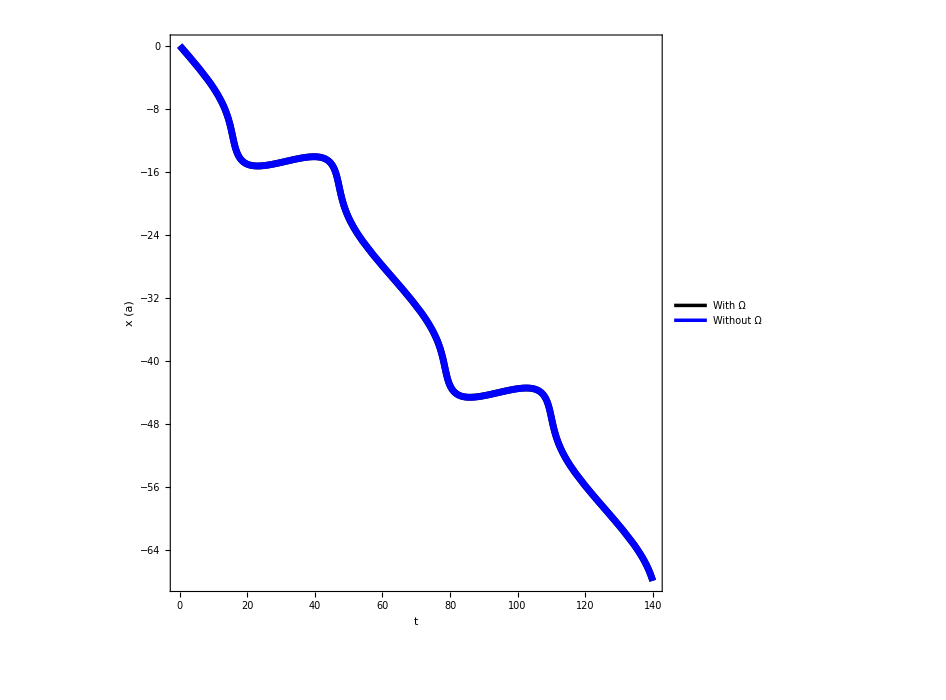

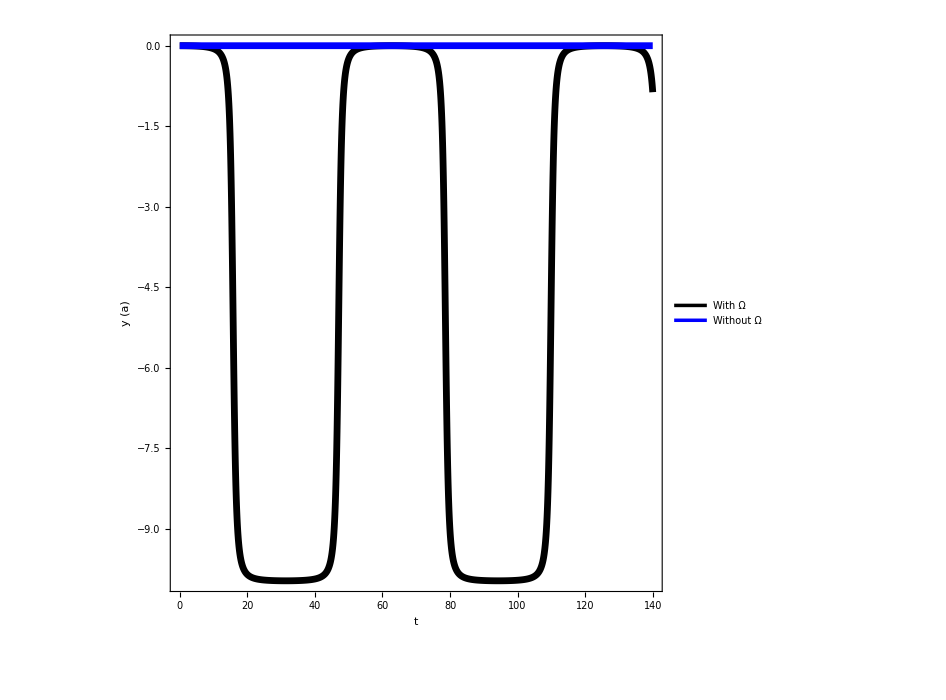

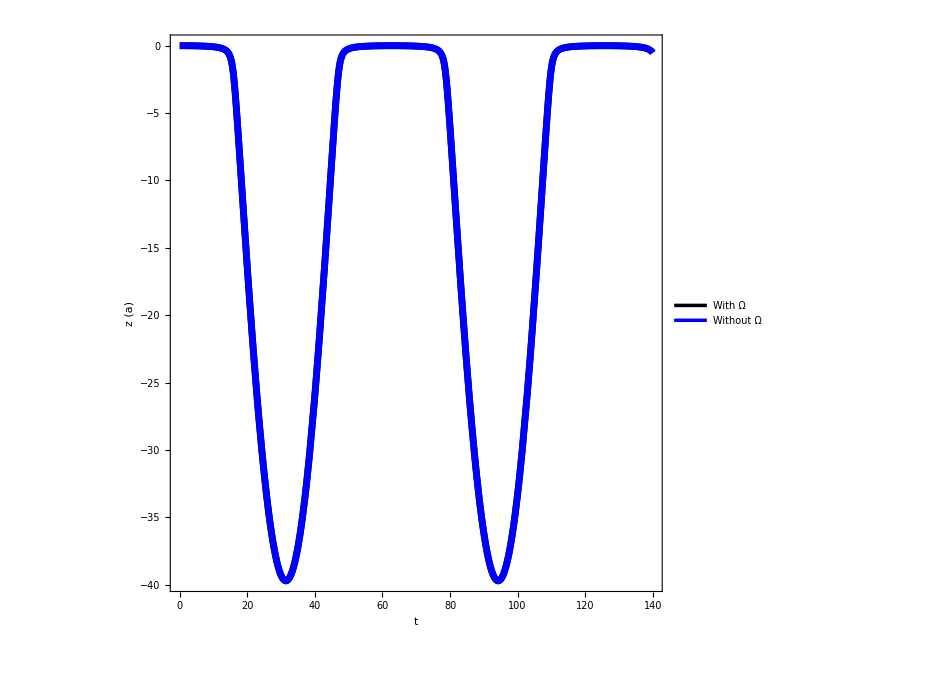

```mathematica
xtPlot=Plot[{newrr[[1]], newrrr[[1]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["x (a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
ytPlot=Plot[{newrr[[2]], newrrr[[2]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["y (a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
ztPlot=Plot[{newrr[[3]], newrrr[[3]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["z (a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
```

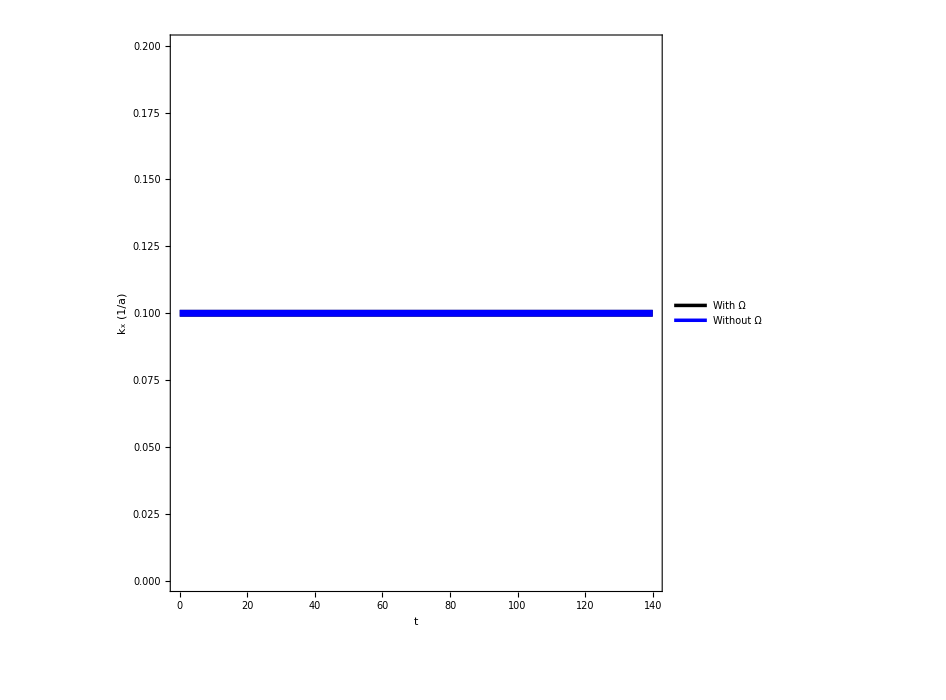

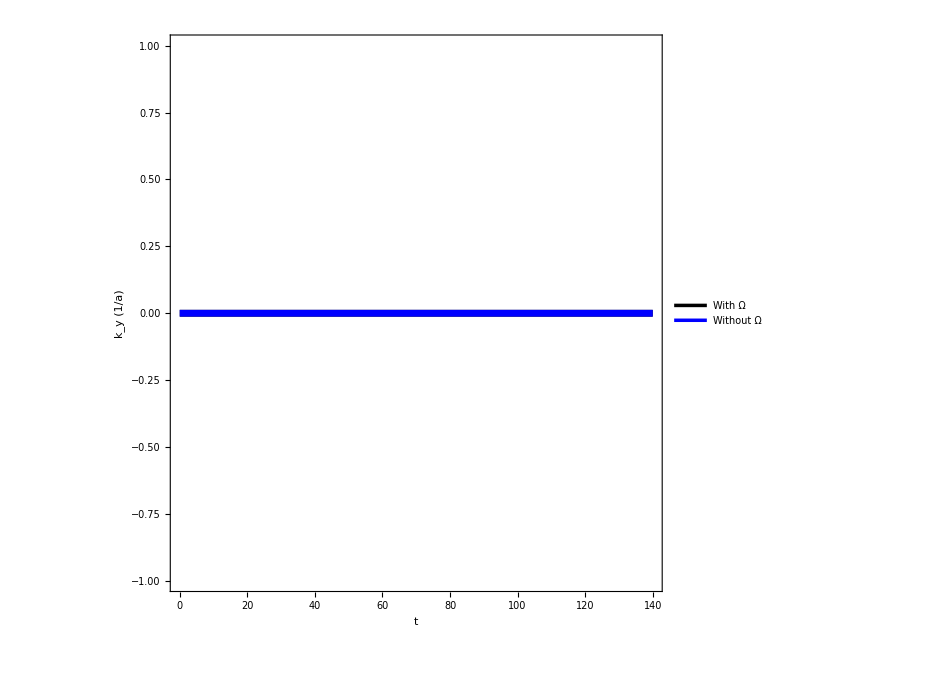

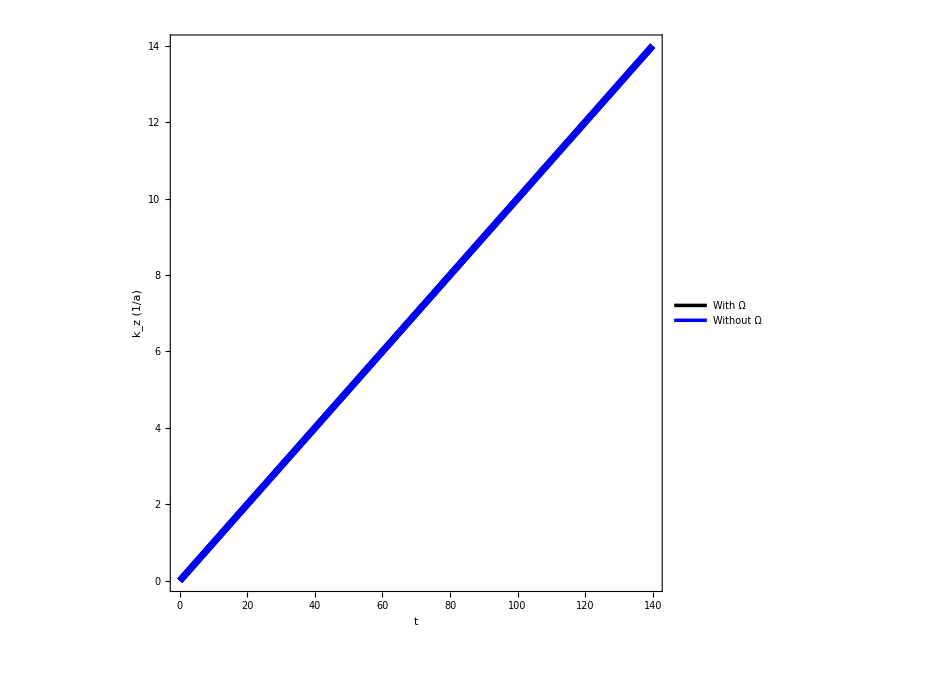

```mathematica
kxtPlot=Plot[{newkk[[1]], newkkk[[1]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["k_x (1/a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
kytPlot=Plot[{newkk[[2]], newkkk[[2]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["k_y (1/a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
kztPlot=Plot[{newkk[[3]], newkkk[[3]]}, {t, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["k_z (1/a)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
```

## Plots of derivatives, ṙ[t] and k̇[t]

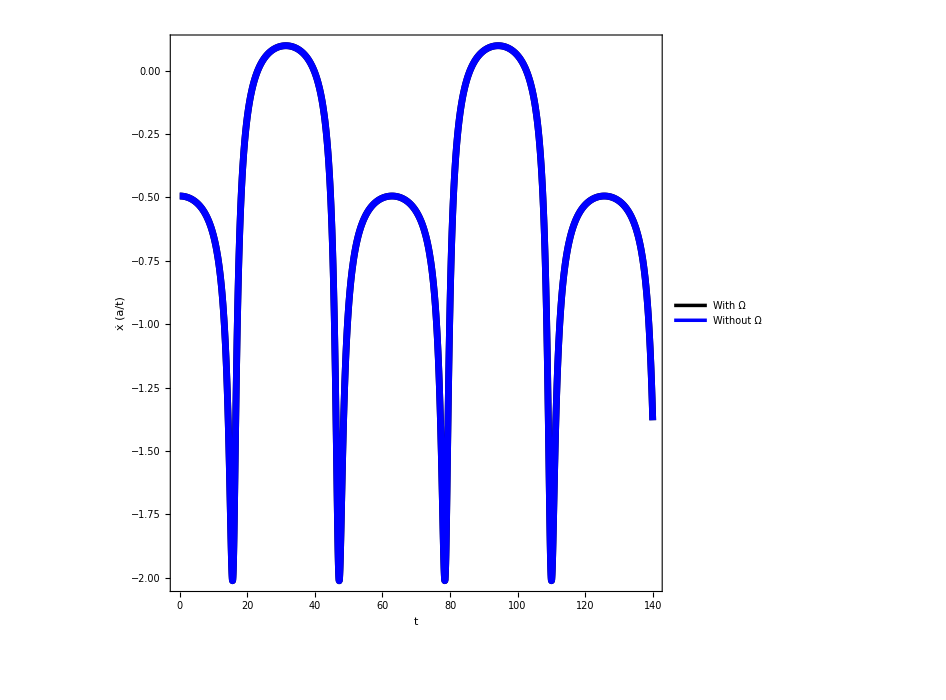

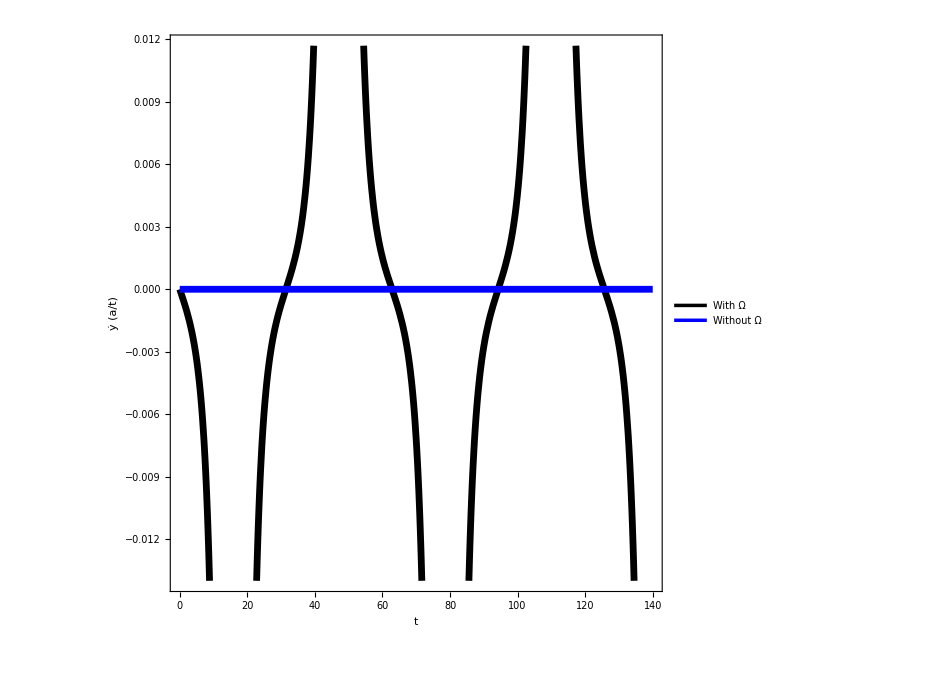

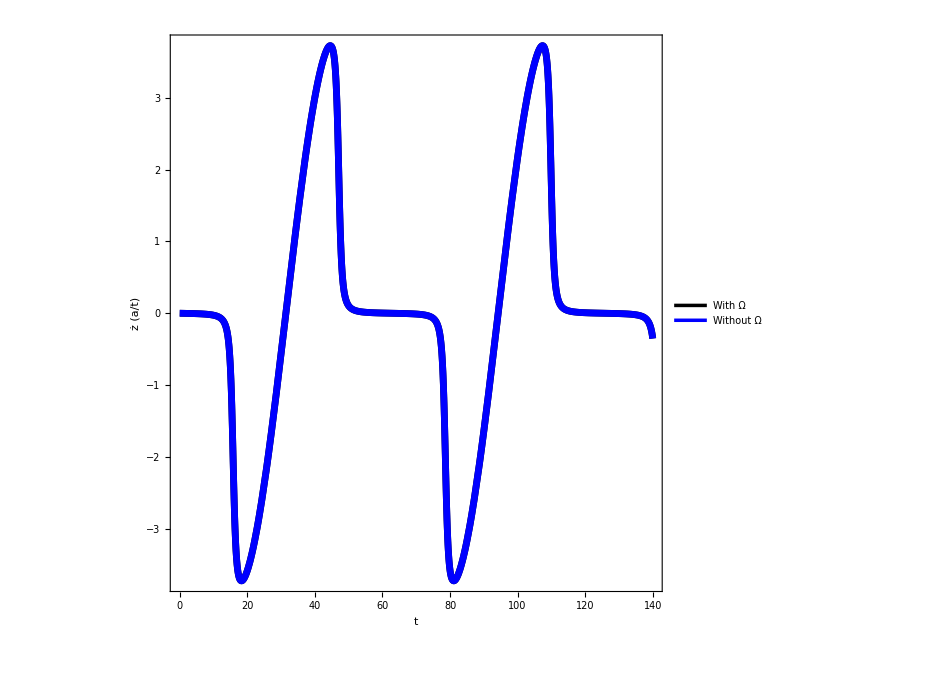

```mathematica
Clear[t];
xdottPlot=Plot[{D[newrr[[1]],t]/.{t->tt}, D[newrrr[[1]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["ẋ (a/t)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
ydottPlot=Plot[{D[newrr[[2]], t]/.{t->tt}, D[newrrr[[2]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["ẏ (a/t)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
zdottPlot=Plot[{D[newrr[[3]], t]/.{t->tt}, D[newrrr[[3]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["ż (a/t)", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
```

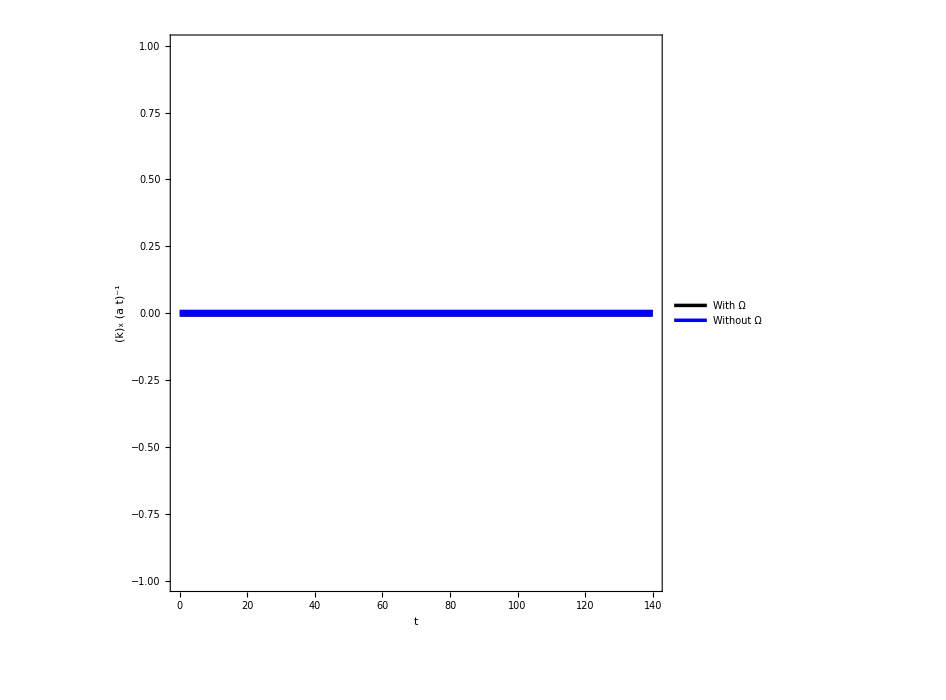

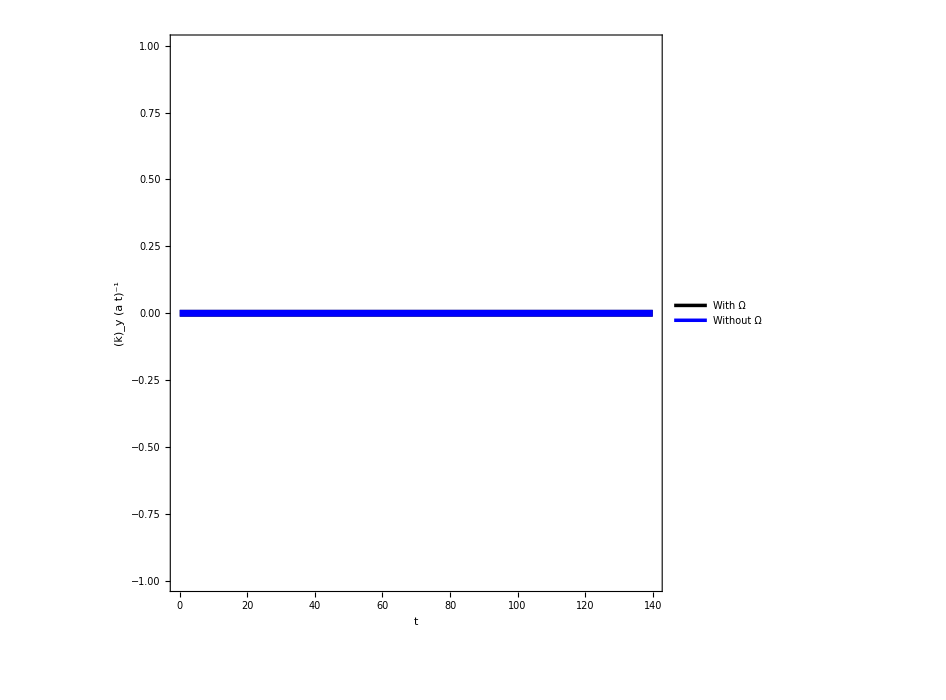

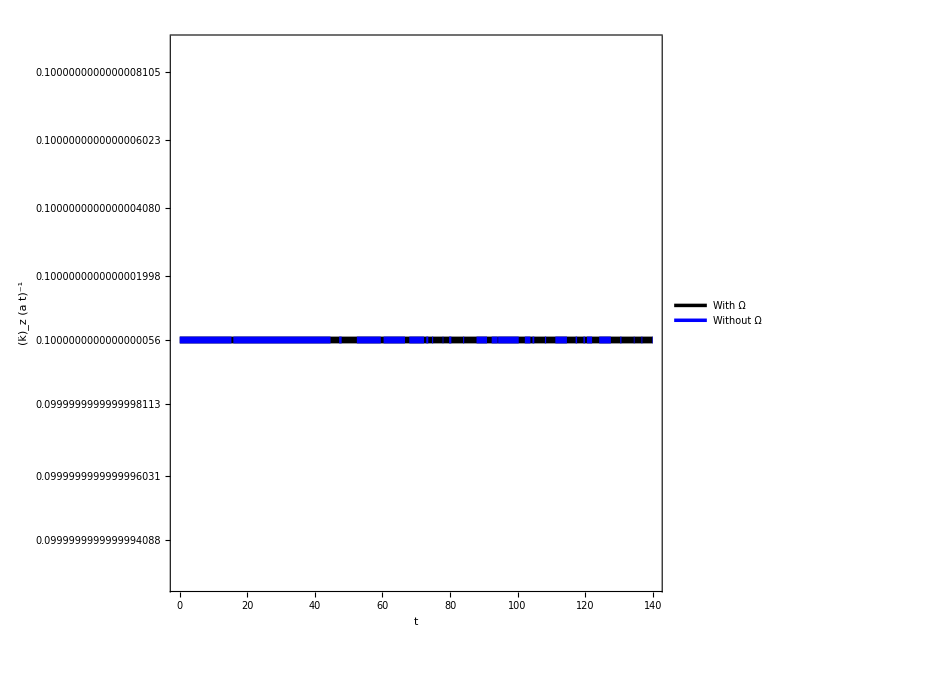

```mathematica
Clear[t];
kxdottPlot=Plot[{D[newkk[[1]],t]/.{t->tt}, D[newkkk[[1]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["(k̇)_x (a t)^-1", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
kydottPlot=Plot[{D[newkk[[2]], t]/.{t->tt}, D[newkkk[[2]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["(k̇)_y (a t)^-1", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
kzdottPlot=Plot[{D[newkk[[3]], t]/.{t->tt}, D[newkkk[[3]], t]/.{t->tt}}, {tt, 0, 140},
ImageSize->{700, 700},
Frame->{{True, False},{True, False}},
FrameTicksStyle->{Directive[Thickness[0.001], Black], Directive[Thickness[0.001], Black]},
RotateLabel->False,
AspectRatio->1,
PlotLegends->{"With Ω", "Without Ω"},
FrameLabel->{Style["t", fontsize, Bold], Style["(k̇)_z (a t)^-1", fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
FrameStyle-> Thickness[0.0015],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
PlotStyle->{{Directive[Thickness[0.007]], Black},{Directive[Thickness[0.007]], Blue}}
]
```

```mathematica
location="/Users/robertmckay/Desktop/Research/Formal Projects/Electron Trajectories for Type II Weyl Semimetals/";
CreateDirectory[location<>"Full Omega Plots, kx=ky=kz=0.1"];
newlocation=location<>"Full Omega Plots, kx=ky=kz=0.1"<>"/";

Export[newlocation<>"x y z Plot.png",xyzPlot];
Export[newlocation<>"kx ky kz Plot.png", kxkykzPlot];
Export[newlocation<>"x t Plot.png", xtPlot];
Export[newlocation<>"y t Plot.png", ytPlot];
Export[newlocation<>"z t Plot.png", ztPlot];
Export[newlocation<>"kx t Plot.png", kxtPlot];
Export[newlocation<>"ky t Plot.png", kytPlot];
Export[newlocation<>"kz t Plot.png", kztPlot];
Export[newlocation<>"xdot t Plot.png", xdottPlot];
Export[newlocation<>"ydot t Plot.png", ydottPlot];
Export[newlocation<>"zdot t Plot.png", zdottPlot];
Export[newlocation<>"kxdot t Plot.png", kxdottPlot];
Export[newlocation<>"kydot t Plot.png", kydottPlot];
Export[newlocation<>"kzdot t Plot.png", kzdottPlot];
```

CreateDirectory::filex: /Users/robertmckay/Desktop/Research/Formal Projects/Electron Trajectories for Type II Weyl Semimetals/Full Omega Plots, kx=ky=kz=0.1 already exists.

```mathematica
(*Example of a dipole

test=D[NDSolve[{x''[t]==(-1)*(x[t]-Pi)/((x[t] - Pi)^2 +y[t]^2)^(3/2)+(1)*(x[t]-Pi/2)/((x[t] - Pi/2)^2 +y[t]^2)^(3/2),
y''[t]==(-1)*y[t]/((x[t] - Pi)^2 +y[t]^2)^(3/2)+(1)*y[t]/((x[t] - Pi/2)^2 +y[t]^2)^(3/2), x[0]==0, y[0]==.1, y'[0]==0.1, x'[0]==0.0}, {x[t], y[t]}, {t, -150, 1000}], t]
Plot[x'[t]/.test[[1]][[1]], {t, -100, 150}]
Plot[y'[t]/.test[[1]][[2]], {t, -100, 150}]
D[x[t]/.test[[1]][[1]], t]
D[y[t]/.test[[1]][[2]], t]*)
```

```mathematica
animationFrame={};
Do[
element1=Take[listrr, UpTo[i]];
element2=Take[listrrr,UpTo[i]];
capPt1=listrr[[i]];
capPt2=listrrr[[i]];
temp=ListPointPlot3D[{element1, element2, {startPointrr}, {capPt1}, {startPointrrr}, {capPt2}},
ImageSize->{700, 700},
PlotStyle->{{Directive[Thickness[0.007], Black], PointSize[Small]}, {Directive[Thickness[0.007], Blue], PointSize[Small]}, {Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]},{Directive[Thickness[0.1], Red], PointSize[Large]}, {Directive[Thickness[0.1], Red], PointSize[Large]}},
PlotLegends->{"With Ω", "Without Ω", "Start Point", "End Point"},
AxesLabel->{Style["x (a)", fontsize, Bold], Style["y (a)", fontsize, Bold], Style["z (a)",fontsize, Bold]},
(*PlotRange->{{0, 20}, {-3, 0}, {0, 5}},
when kx0=0.01*)
AxesStyle->Thickness[0.002],
TicksStyle->{Directive[fontsize - 8,Bold], Directive[fontsize - 8,Bold]},
ViewPoint->{-Infinity, -Infinity, Infinity}
(*PlotRange->{{-1, 20}, {0, 1}, {0, 1}}*)
];
AppendTo[animationFrame, temp],
{i, 1, Length@listrr}]
```

```mathematica
ListAnimate[animationFrame
]
```

ListAnimate[animationFrame]